```mathematica
files = FileNames["*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
filterdata = data[[ ;; 13]];
foehndata = data[[14 ;; ]];
```

```mathematica
fitrange={{0,0.00252},{0,0.0045},{0,0.0053},{0,0.0047},{0,0.003},{0,0.0038},{0,0.007},{0,0.0064},{0,0.008},{0,0.01},{0,0.01},{0,0.02},{0,0.04}};
fitdata =Table[Select[filterdata[[i, 1]], #[[1]]≥ fitrange[[i,1]] && #[[1]]≤fitrange[[i,2]]&],{i,{1,2,3,4,5,6,7,8,9,10,11,12,13}}];
```

```mathematica
ListPlot[filterdata[[#,1]]&/@Range[13],ImageSize->900,Frame->True]
```

## nlm

```mathematica
startval={{
{a,1.22},{b,-0.05},{μ,0.7},{σ,15},{c,0.1},{d,1}},
{{a,1},{b,0},{μ,1},{σ,10},{c,0.2},{d,7}},
{{a,1.22},{b,-0.05},{μ,1.7},{σ,10},{c,0.15},{d,2}},
{{a,1.22},{b,-0.05},{μ,2.7},{σ,10},{c,0.2},{d,1}},
{{a,1.2},{b,-0.05},{μ,1.3},{σ,10},{c,0.15},{d,1}},
{{a,1.2},{b,-0.05},{μ,1.3},{σ,10},{c,0.15},{d,1}},
{{a,1.5},{b,-0.05},{μ,3.4},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,4.3},{σ,10},{c,0.15},{d,10}},
{{a,1.2},{b,-0.05},{μ,5.4},{σ,20},{c,0.2},{d,1}},
{{a,1.5},{b,-0.05},{μ,6.6},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,5.1},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,11},{σ,10},{c,0.15},{d,10}},
{{a,1},{b,-0.05},{μ,30},{σ,76},{c,0.15},{d,1}}
};
Conμup={3,3,3,3,3,3,4,5,6,7,7,12,40};
Conddown={1,1,1,0.1,1,1,0.1,0.1,0.1,0.1,0.1,0.1,0.02};
Conσup={100,100,100,100,100,100,19.5,100,100,100,100,100,100};
Concdown={0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.1};
Conaup={2,2,2,2,2,2,2,2,2,2,2,2,1.18};
Condup={100,100,100,100,100,100,100,100,100,100,100,100,100};
fitvals={};
nlms={};
Do[
nlm= NonlinearModelFit[fitdata[[n]],
{a/(1+Exp[(-x+μ*10^-3)/(σ*10^-6)])+b+Piecewise[{{0,x<μ*10^-3},{ c(1- Exp[-d*10^3 (x-μ*10^-3)]),x≥μ*10^-3}}],
0.1<a,a<Conaup[[n]],-1<b,b<1,0.5<μ,μ<Conμup[[n]],0.1<σ,σ<Conσup[[n]],Concdown[[n]]<c,c<10,Conddown[[n]]<d,d<Condup[[n]]}, startval[[n]], x];
Quiet[fitvals=Append[fitvals,nlm["ParameterTableEntries"]]];
nlms=Append[nlms,nlm];
Print[n];
Quiet[Print[nlm["ParameterTable"]]],
{n,1,13}]
```

1

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.25176 | 0.00307217 | 407.451 | 2.17231509998×10^-1116
b | -0.0659128 | 0.000748048 | -88.1131 | 1.74628778617×10^-474
μ | 0.71396 | 0.000149643 | 4771.08 | 7.78653604849×10^-2187
σ | 11.5799 | 0.125073 | 92.5854 | 1.08432215918×10^-493
c | 0.136855 | 0.00270619 | 50.5711 | 3.52014×10^-278
d | 2.8771 | 0.105677 | 27.2253 | 1.19105×10^-122

2

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.26605 | 0.00141804 | 892.819 | 2.00157110375×10^-2379
b | -0.0640796 | 0.000324495 | -197.475 | 6.66297515348×10^-1220
μ | 1.84252 | 0.000104956 | 17555.1 | 1.231817574×10^-4700
σ | 13.1647 | 0.0899851 | 146.298 | 6.62405167667×10^-1000
c | 0.139015 | 0.00119606 | 116.228 | 9.23914500824×10^-838
d | 1.39927 | 0.0311633 | 44.9014 | 8.70606×10^-296

3

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.2292 | 0.00242387 | 507.124 | 3.99864559055×10^-852
b | -0.0640705 | 0.000402024 | -159.37 | 4.17344325452×10^-526
μ | 1.68864 | 0.000139694 | 12088.2 | 7.33963044242×10^-1754
σ | 13.6718 | 0.116144 | 117.715 | 7.24078968455×10^-443
c | 0.148154 | 0.0020247 | 73.1733 | 1.87143103838×10^-317
d | 2.32942 | 0.0783473 | 29.732 | 1.29694×10^-123

4

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.23826 | 0.00169793 | 729.277 | 1.28861039932×10^-1290
b | -0.0637374 | 0.000267606 | -238.176 | 3.58812567832×10^-839
μ | 2.74401 | 0.000119545 | 22953.9 | 7.41376825159×10^-2691
σ | 14.8845 | 0.100837 | 147.61 | 4.23227171872×10^-650
c | 0.152197 | 0.00140167 | 108.583 | 2.27198383248×10^-532
d | 1.66101 | 0.0444627 | 37.3574 | 1.23804×10^-187

5

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.21016 | 0.00272399 | 444.259 | 6.56682409560957×10^-419
b | -0.0634134 | 0.000577096 | -109.884 | 2.23385×10^-241
μ | 1.30666 | 0.000195006 | 6700.59 | 1.82640181891258×10^-766
σ | 16.5476 | 0.162749 | 101.675 | 1.09815×10^-231
c | 0.164209 | 0.00220157 | 74.587 | 1.70246×10^-193
d | 1.63866 | 0.0734103 | 22.3219 | 2.51902×10^-65

6

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.21878 | 0.00324367 | 375.742 | 2.7951795711×10^-485
b | -0.06333 | 0.000461565 | -137.207 | 1.34122157193×10^-322
μ | 2.40055 | 0.000220301 | 10896.7 | 1.82117362021×10^-1033
σ | 16.9587 | 0.180839 | 93.7775 | 2.07605×10^-262
c | 0.158439 | 0.00286807 | 55.2426 | 3.02176×10^-182
d | 1.68908 | 0.111055 | 15.2095 | 4.95686×10^-41

7

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.20768 | 0.00313818 | 384.835 | 3.97428016145×10^-812
b | -0.0633122 | 0.000604027 | -104.817 | 4.23979171818×10^-428
μ | 3.41941 | 0.000342818 | 9974.41 | 6.96523755298×10^-1794
σ | 19.5 | 0.293225 | 66.5019 | 1.60125×10^-303
c | 0.194956 | 0.00265918 | 73.3144 | 2.74645556317×10^-329
d | 1.03549 | 0.0363556 | 28.4822 | 7.69739×10^-119

8

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.19653 | 0.00250938 | 476.821 | 1.74344015177×10^-813
b | -0.0641571 | 0.000337251 | -190.235 | 4.33046995775×10^-562
μ | 4.35379 | 0.000223189 | 19507.2 | 1.27938661749×10^-1836
σ | 18.7944 | 0.187321 | 100.333 | 1.10500522805×10^-391
c | 0.183527 | 0.00219846 | 83.4799 | 1.48228426224×10^-344
d | 1.24541 | 0.052065 | 23.9202 | 1.20231×10^-90

9

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.20244 | 0.00212488 | 565.887 | 3.16147295798×10^-1038
b | -0.0632052 | 0.000297587 | -212.392 | 1.82308666901×10^-702
μ | 5.4005 | 0.000225861 | 23910.8 | 2.31955072838×10^-2330
σ | 20.8138 | 0.191005 | 108.97 | 3.28342151364×10^-480
c | 0.19096 | 0.00189576 | 100.73 | 6.75448460566×10^-455
d | 0.988046 | 0.0338584 | 29.1817 | 7.92795×10^-128

10

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.20161 | 0.00183922 | 653.323 | 1.84002548715×10^-1312
b | -0.0638948 | 0.000262443 | -243.461 | 5.3607981701×10^-889
μ | 6.62877 | 0.000221444 | 29934.3 | 1.07389058979×10^-2964
σ | 21.6913 | 0.189014 | 114.76 | 4.03872676257×10^-576
c | 0.198681 | 0.00156052 | 127.317 | 3.97718246466×10^-618
d | 0.8842 | 0.0218747 | 40.4211 | 3.87396×10^-212

11

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.19399 | 0.00347217 | 343.875 | 1.853379377114×10^-491
b | -0.063061 | 0.000652223 | -96.6862 | 4.69409×10^-277
μ | 5.12684 | 0.000557252 | 9200.22 | 5.377978535909×10^-1055
σ | 28.4853 | 0.474702 | 60.0068 | 1.37018×10^-200
c | 0.213713 | 0.00290982 | 73.4456 | 2.13129×10^-232
d | 0.695183 | 0.0265326 | 26.2011 | 2.03866×10^-88

12

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.18657 | 0.00287856 | 412.209 | 3.34184532452×10^-929
b | -0.0631721 | 0.000407957 | -154.85 | 5.55685940677×10^-596
μ | 11.1135 | 0.000577922 | 19230.1 | 3.82369085783×10^-2255
σ | 35.6017 | 0.493115 | 72.1976 | 2.22623156744×10^-351
c | 0.219425 | 0.00266581 | 82.3109 | 2.68474085235×10^-391
d | 0.664392 | 0.0143369 | 46.3415 | 3.97283×10^-228

13

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.18 | 0.00551549 | 213.943 | 6.19172339514×10^-705
b | -0.0622564 | 0.000426451 | -145.987 | 2.52570857973×10^-576
μ | 29.742 | 0.00155995 | 19066. | 3.47917016134×10^-2252
σ | 72.7395 | 1.27174 | 57.197 | 5.36299×10^-284
c | 0.225685 | 0.00515878 | 43.7477 | 7.75829×10^-214
d | 0.606585 | 0.0219544 | 27.6294 | 2.59457×10^-118

## nlm2

```mathematica
startval={{
{a,1.22},{b,-0.05},{μ,0.7},{σ,15},{c,0.1},{d,1}},
{{a,1},{b,0},{μ,1},{σ,10},{c,0.2},{d,7}},
{{a,1.22},{b,-0.05},{μ,1.7},{σ,10},{c,0.15},{d,2}},
{{a,1.22},{b,-0.05},{μ,2.7},{σ,10},{c,0.2},{d,1}},
{{a,1.2},{b,-0.05},{μ,1.3},{σ,10},{c,0.15},{d,1}},
{{a,1.2},{b,-0.05},{μ,1.3},{σ,10},{c,0.15},{d,1}},
{{a,1.5},{b,-0.05},{μ,3.4},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,4.3},{σ,10},{c,0.15},{d,10}},
{{a,1.2},{b,-0.05},{μ,5.4},{σ,20},{c,0.2},{d,1}},
{{a,1.5},{b,-0.05},{μ,6.6},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,5.1},{σ,10},{c,0.15},{d,10}},
{{a,1.5},{b,-0.05},{μ,11},{σ,10},{c,0.15},{d,10}},
{{a,1},{b,-0.05},{μ,30},{σ,76},{c,0.15},{d,1}}
};
Conμup={3,3,3,3,3,3,4,5,6,7,7,12,40};
Conddown={1,1,1,0.1,1,1,0.1,0.1,0.1,0.1,0.1,0.1,0.02};
Conσup={100,100,100,100,100,100,19.5,100,100,100,100,100,100};
Concdown={0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.001,0.1};
Conaup={2,2,2,2,2,2,2,2,2,2,2,2,1.18};
Condup={100,100,100,100,100,100,100,100,100,100,100,100,100};
fitvals2={};
nlms2={};
Do[
nlm= NonlinearModelFit[fitdata[[n]],
{a/(1+Exp[(-x+μ*10^-3)/(σ*10^-6)])+b+Piecewise[{{0,x<μ*10^-3},{ c(1- Exp[-d*10^3 (x-μ*10^-3)]),x≥μ*10^-3}}],
0.1<a,a<Conaup[[n]],-1<b,b<1,0.5<μ,μ<Conμup[[n]],0.1<σ,σ<Conσup[[n]],Concdown[[n]]<c,c<10,Conddown[[n]]<d,d<Condup[[n]]}, startval[[n]], x];
Quiet[fitvals2=Append[fitvals2,nlm["ParameterTableEntries"]]];
nlms2=Append[nlms2,nlm];
Print[n];
Quiet[Print[nlm["ParameterTable"]]],
{n,{3}}]
nlms[[3]]=nlm;
Quiet[fitvals[[3]]=nlm["ParameterTableEntries"]];
```

3

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.2555 | 0.00142603 | 880.421 | 1.57121247593×10^-1514
b | -0.0641998 | 0.000383166 | -167.551 | 1.73005055261×10^-762
μ | 1.68946 | 0.00012314 | 13719.8 | 1.78339696438×10^-2772
σ | 14.2953 | 0.106098 | 134.737 | 4.14934573713×10^-667
c | 0.152559 | 0.00122305 | 124.736 | 7.38901892234×10^-634
d | 1.18893 | 0.0217701 | 54.613 | 9.83336738003×10^-310

{1.87904,2.99648,4.01354,5.02499,5.99934,7.06545,8.05059,9.02621,10.0095,11.2312,16.7332,22.6465,52.018}

{1.18082,1.19111,1.16714,1.1498,1.10936,1.12367,1.07604,1.07716,1.07469,1.06682,1.04334,1.03032,1.01657}

| Estimate | Standard Error | t-Statistic | P-Value
a | 7.32522 | 1.21313 | 6.03827 | 0.000125548
min | 1.01608 | 0.0111339 | 91.2599 | 6.1082×10^-16
amp | 0.239412 | 0.0184113 | 13.0036 | 1.36794×10^-7

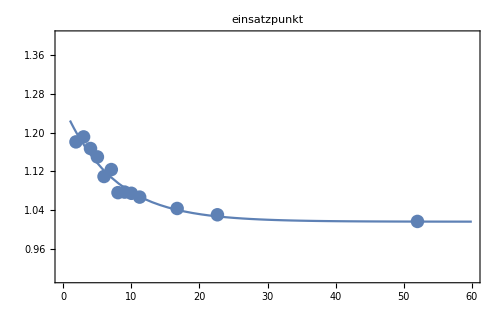

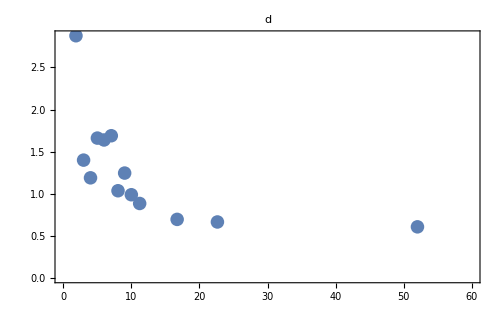

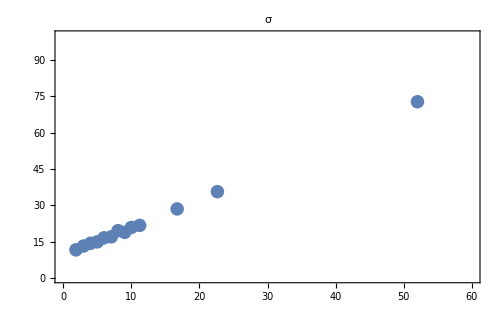

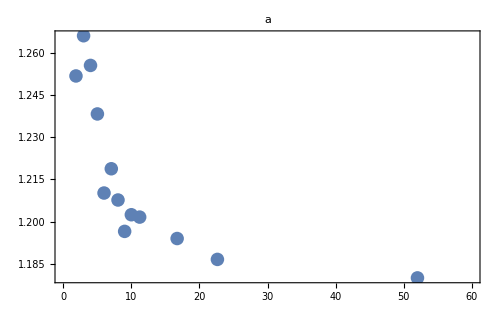

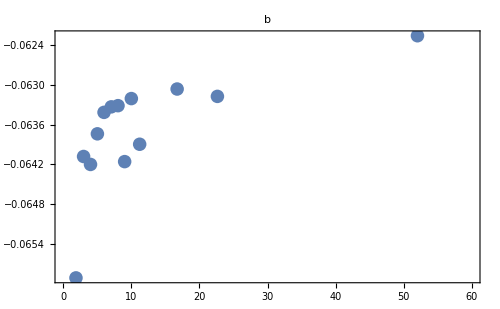

| Estimate | Standard Error | t-Statistic | P-Value
min | 0.10613 | 0.00993473 | 10.6827 | 8.64991×10^-7
amp | 0.122683 | 0.00975232 | 12.5799 | 1.87212×10^-7
a | 8.78399 | 1.62551 | 5.40384 | 0.000299784

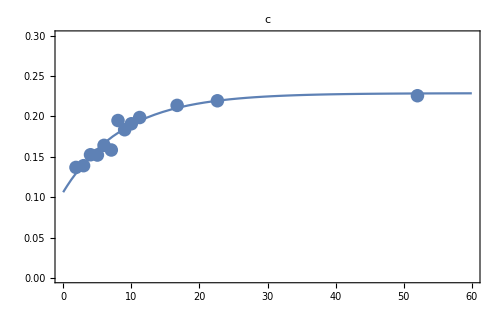

```mathematica
steigpunkt=fitvals[[All,3,1]];
fallpunkt={{{0.002593,0.6409}},{{0.004839,0.6786}},{{0.005703,0.6157}},{{0.007769,0.7189}},{{0.007306,0.7321}},{{0.009466,0.7529}},{{0.01147,0.7529}},{{0.01338,0.672}},{{0.01541,0.6945}},{{0.01786,0.6394}},{{0.02186,0.6795}},{{0.03376,0.6269}},{{0.08176,0.647}}}[[All,1,1]]*10^3;
T=fallpunkt-steigpunkt

einsatzpunkt=fitvals[[All,1,1]]-fitvals[[All,2,1]]-fitvals[[All,5,1]]

nlmeinsatzpunkt=NonlinearModelFit[Transpose[{T,einsatzpunkt}],{min+amp Exp[-x/a],0<amp,amp<1,0<min,0<a},{a,min,amp},x];
Quiet[nlmeinsatzpunkt["ParameterTable"]]
Show[Plot[Normal[nlmeinsatzpunkt],{x,1,60},PlotLabel->"einsatzpunkt",Frame->True,PlotRange->{{0,60},{0.9,1.4}},ImageSize->500],ListPlot[Transpose[{T,einsatzpunkt}]]]


ListPlot[Transpose[{T,fitvals[[All,6,1]]}],PlotLabel->"d",Frame->True,PlotRange->{{0,60},Automatic}]
ListPlot[Transpose[{T,fitvals[[All,4,1]]}],PlotLabel->"σ",Frame->True,PlotRange->{{0,60},{0,100}}]
ListPlot[Transpose[{T,fitvals[[All,1,1]]}],PlotLabel->"a",Frame->True,PlotRange->{{0,60},Automatic}]
ListPlot[Transpose[{T,fitvals[[All,2,1]]}],PlotLabel->"b",Frame->True,PlotRange->{{0,60},Automatic}]


nlmc=NonlinearModelFit[Transpose[{T,fitvals[[All,5,1]]}],{min+amp(1- Exp[-x/a]),0<min,0<amp,0<a},{min,amp,a},x];
Quiet[nlmc["ParameterTable"]]
Show[Plot[Normal[nlmc],{x,0,60},PlotLabel->"c",Frame->True,PlotRange->{{0,60},{0,0.3}}],ListPlot[Transpose[{T,fitvals[[All,5,1]]}]]]
```

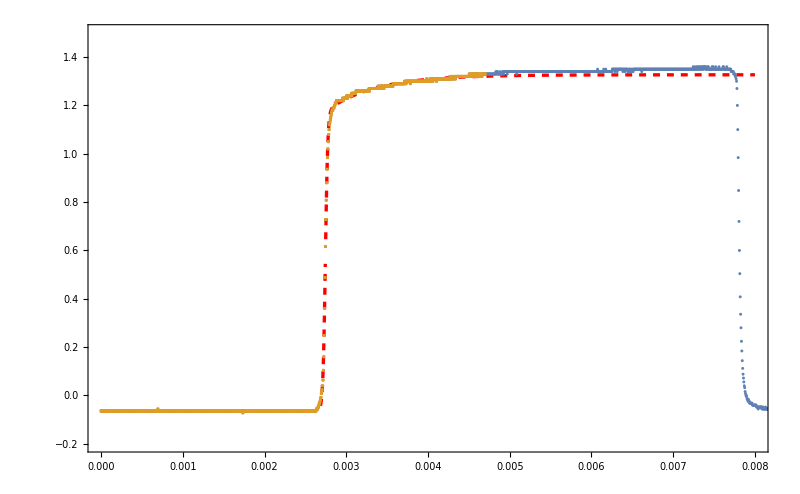

```mathematica
nr=4;
Show[Plot[Normal[nlms[[nr]]],{x,0,0.008},ImageSize->800,Frame->True,PlotRange->{-0.2,1.5},ImageSize->500,Frame->True, PlotStyle->{Red, Dashed,Thickness->0.003}],ListPlot[{filterdata[[nr,1]],fitdata[[nr]]},PlotMarkers->{Automatic,3}]]
```

```mathematica
Manipulate[Show[Plot[{Normal[nlm],a/(1+Exp[(-x+μ*10^-3)/(σ*10^-6)])+b+Piecewise[{{0,x<μ*10^-3},{ c(1- Exp[-d*10^3 (x-μ*10^-3)]),x≥μ*10^-3}}]},{x,0,0.01},ImageSize->600,Frame->True,PlotRange->{-0.2,1.5},Frame->True, PlotStyle->{Red, Dashed,3}],ListPlot[{filterdata[[n,1]],fitdata[[n]]},PlotMarkers->{Automatic,1}]],{{a,1.23},0,5},{{b,0.05},-2,2},{{μ,1.8},0.7,3},{{σ,10},1,20},{{c,0.11},0,2},{{d,9300},0,10000}]
```